## QCD Parameters

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

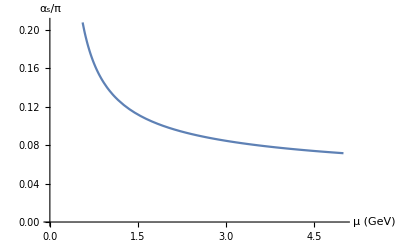

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

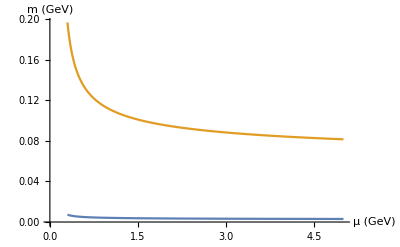

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.07;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=8.2 αGG
```

0.574

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[s_,k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Holder Inequalities

```mathematica
holder[s_,alpha_,beta_,τ_,τ1_,τ2_,s0_,jpc_?StringQ,flavor_?StringQ]:=If[(gaussian[s,alpha/ω,τ1,s0,jpc,flavor]>0)&&(Im[gaussian[s,alpha/ω,τ1,s0,jpc,flavor]]==0),
Max[Table[gaussian[s,alpha+beta,τ,s0,jpc,flavor]/((τ1/τ)^(ω/2)(τ2/τ)^((1-ω)/2)gaussian[s,alpha/ω,τ1,s0,jpc,flavor]^ω gaussian[s,beta/(1-ω),τ2,s0,jpc,flavor]^(1-ω)),{ω,0.1,0.9,0.1}]],2]
(*ADD IF STATEMENT on Subscript[G, k](Subscript[τ, 1],s)*)
```

## Procedure

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
alpha=ω;
beta=1-ω;
s0=10000;
jpc="0-+";
flavor="light";
τ1=τ;
τ2=τ+δτ;
δτ=0.1;
(*END PARAMETERS*)

(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor,s0,alpha,beta,τ1,τ2,δτ,ω];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
alpha=0;
beta=0;
s0=10000;
τ1=τ;
τ2=τ+δτ;
δτ=0.1;

holderTable[jpc,flavor]=Table[{τ,s,holder[s,alpha,beta,(τ1 τ2)/(τ2 ω+τ1(1-ω)),τ1,τ2,s0,jpc,flavor]},{τ,0,100,2},{s,-100,50,2}];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-holderInequality",ToString[flavor],"_",
ToString[jpc]];
input=holderTable[jpc,flavor];
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
]
]
(*END LOOP*)
```

Greater::nord: Invalid comparison with -1.29316580324672×10^217107-4.47190162549761×10^217107 ⅈ attempted.

Greater::nord: Invalid comparison with -4.88386751518184×10^217063-1.68889209914328×10^217064 ⅈ attempted.

Greater::nord: Invalid comparison with -1.86301557786741×10^217020-6.44250131736831×10^217020 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.